## Block’s stuff

```mathematica
swapLR[p_]:=Module[{pnew},
pnew=Table[0,{20}];
(*swap normal forces*)
pnew[[1;;4;;2]]=p[[17;;20;;2]];pnew[[17;;20;;2]]=p[[1;;4;;2]];(*Ls--Ld*)
pnew[[5;;9;;2]]=p[[9;;5;;-2]];(*Ns--Nc--Nd*)
pnew[[11;;15;;2]]=p[[15;;11;;-2]];(*Rs--Rc--Rd*)
(*swap tangential forces*)
pnew[[2;;4;;2]]=-p[[18;;20;;2]];pnew[[18;;20;;2]]=-p[[2;;4;;2]];(*Vsu--Vdu,Vsb--Vdb*)
pnew[[6;;10;;2]]=-p[[10;;6;;-2]];(*Ts--Td*)
pnew[[12;;16;;2]]=-p[[16;;12;;-2]];(*Vs--Vc--Vd*)

pnew
];
```

```mathematica
V[H_,Rt_,μ_,R_]:=Piecewise[{{R/Rt H,Abs[H]<=μ Rt},{Sign[H]μ R,Abs[H]>μ Rt}}];
```

```mathematica
solveBlockL2R[pBlock_,contact_]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,Ms,Mc,Md,H,Rt},
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=pBlock;

(*solution left to right*)
Ldu=0;Vdu=0;Ldb=0;Vdb=0;
Md=(Ns+Vsu+Vsb+Nc/2+P/2)b-h(Lsu-Ldu+Ts+Tc+Td);
Ms=(Nc/2+P/2+Nd-Vdu-Vdb)b+h(Lsu-Ldu+Ts+Tc+Td);
Mc=(Ns+Vsu+Vsb-Nd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td);
Rt=Vsu+Vsb+Ns+Nc+P+Nd-Vdu-Vdb;
H=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb;

If[contact==1,
(*mechanism 1*)
Rc=0;
Rs=Max[Md/b,0];
Rd=Rt-Rs;,
(*mechanism 2 or 3*)
Rs=Max[Mc/(b/2),0];
Rd=Piecewise[{{Max[-Mc/(b/2),0],Md>=0},{Rt,Md<0}}];
Rc=Piecewise[{{Max[Rt-Rs-Rd,0],Md>=0},{0,Md<0}}];
];

Ldu=Max[-Md/h,0];
Vs=V[H,Rt,μ,Rs];
Vc=V[H,Rt,μ,Rc];
Vd=Piecewise[{{V[H,Rt,μ,Rd],Md>=0},{Min[H-Ldu,μ Rd],Md<0}}];
Ldb=H-Ldu-Vs-Vc-Vd;

{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}
];
```

```mathematica
solveHalvedBlockL2R[pBlock_,isOnLeftEdge_]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,Ms,Mc,Md,H,Rt},
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=pBlock;

(*solution left to right*)
Ldu=0;Vdu=0;Ldb=0;Vdb=0;
Rt=Vsu+Vsb+Ns+Nc+P/2+Nd-Vdu-Vdb;
H=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb;

(*modify resultants for the halved block*)
If[isOnLeftEdge,
(*halved block on the left edge*)
Md=(Ns+Vsu+Vsb+Nc/2+P/2/4)b-h(Lsu-Ldu+Ts+Tc+Td);
Mc=(Ns+Vsu+Vsb-Nd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td)-P/2b/4;
(*compute reactions for the halved block - only one mechanism*)
Rs=0;
Rd=Piecewise[{{Max[-Mc/(b/2),0],Md>=0},{Rt,Md<0}}];
Rc=Piecewise[{{Max[Rt-Rs-Rd,0],Md>=0},{0,Md<0}}];,
(*halved block on the right edge*)
Ms=(Nc/2+P/2/4+Nd-Vdu-Vdb)b+h(Lsu-Ldu+Ts+Tc+Td);
Md=(Ns+Vsu+Vsb-Nd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td)+P/2b/4;
(*compute reactions for the halved block - only one mechanism*)
Rd=0;
Rc=Piecewise[{{Max[Ms/(b/2),0],Md>=0},{Rt,Md<0}}];
Rs=Piecewise[{{Max[Rt-Rc-Rd,0],Md>=0},{0,Md<0}}];
];

Ldu=Max[-Md/h,0];
Vs=V[H,Rt,μ,Rs];
Ldu=Max[-Md/h,0];
Vs=V[H,Rt,μ,Rs];
If[isOnLeftEdge,
Vc=V[H,Rt,μ,Rc];
Vd=Piecewise[{{V[H,Rt,μ,Rd],Md>=0},{Min[H-Ldu,μ Rd],Md<0}}];
Ldb=Piecewise[{{Max[H-μ Rt,0],Md>=0},{H-Ldu-Vd,Md<0}}];,
Vd=0;
Vc=Piecewise[{{V[H,Rt,μ,Rc],Md>=0},{Min[H-Ldu,μ Rc],Md<0}}];
Ldb=Piecewise[{{Max[H-μ Rt,0],Md>=0},{H-Ldu-Vc,Md<0}}];
];

{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}
];
```

```mathematica
solveBlockR2L[pBlock_,contact_]:=Module[{},
swapLR[solveBlockL2R[swapLR[pBlock],contact]]
];

solveHalvedBlockR2L[pBlock_,isOnLeftEdge_]:=Module[{},
swapLR[solveHalvedBlockL2R[swapLR[pBlock],!isOnLeftEdge]]
];
```

```mathematica
solveBlock[pBlock_,contact_,{nRow_,j_},dir_]:=Module[{},
If[!isBlockHalved[{nRow,j}],
(*normal blocks*)
If[dir>0,
solveBlockL2R[pBlock,contact],
solveBlockR2L[pBlock,contact]
],
(*halved blocks*)
If[dir>0,
solveHalvedBlockL2R[pBlock,isBlockOnLeftEdge[{nRow,j}]],
solveHalvedBlockR2L[pBlock,isBlockOnLeftEdge[{nRow,j}]]
]
]
];
```

```mathematica
correctBlock[pBlock_,contact_,{nRow_,j_}]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,Mc,Md,H,Rt},
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=pBlock;

If[isBlockHalved[{nRow,j}],
(*halved blocks*)
If[isBlockOnLeftEdge[{nRow,j}],
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=solveHalvedBlockR2L[pBlock,True];,
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=solveHalvedBlockL2R[pBlock,False];
];,
(*normal blocks*)
Rt=Vsu+Vsb+Ns+Nc+P+Nd-Vdu-Vdb;
H=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb;
Md=(Ns+Vsu+Vsb+Nc/2+P/2)b-h(Lsu-Ldu+Ts+Tc+Td);
Mc=(Ns+Vsu+Vsb-Nd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td);

If[Abs[Mc/Rt]>b/2,
(*no base mechanism is possible, solve L2R or R2L*)
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=solveBlock[pBlock,contact,{nRow,j},-Sign[Mc/Rt]];
,
(*base mechanism is possible*)
If[contact==1,
(*meccanismo 1*)
Rc=0;
Rs=Md/b;
Rd=Rt-Rs;,
(*meccanismo 2 e 3*)
Rs=Max[Mc/(b/2),0];
Rd=Max[-Mc/(b/2),0];
Rc=Rt-Rs-Rd;
];
Vs=V[H,Rt,μ,Rs];
Vd=V[H,Rt,μ,Rd];
Vc=V[H,Rt,μ,Rc];
(*check if the friction criterion is satisfied*)
If[H-Vs-Vc-Vd>0,
Ldb=H+Ldb-Vs-Vc-Vd;
];
If[H-Vs-Vc-Vd<0,
Lsb=-(H-Lsb-Vs-Vc-Vd);
];
];
];

{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}
];
```

## Wall’s stuff

```mathematica
getBlockNum[{nRow_,j_}]:=Module[{nBlock},
If[EvenQ[nRow],
nBlock=nelx nRow/2+(nelx-1)(nRow/2-1);,
nBlock=nelx (nRow-1)/2+(nelx-1)(nRow-1)/2;
];

nBlock+=j
];

getTotalBlocksInRow[nRow_]:=Module[{},
If[EvenQ[nRow],
nelx-1,
nelx
]
];

isBlockOnRightEdge[{nRow_,j_}]:=Module[{},
If[EvenQ[nRow],
j==nelx-1,
j==nelx]
];

isBlockOnLeftEdge[{nRow_,j_}]:=j==1;

isBlockHalved[{nRow_,j_}]:=OddQ[nRow]&&(isBlockOnLeftEdge[{nRow,j}]||isBlockOnRightEdge[{nRow,j}]);
```

```mathematica
getBlockLoads[{nRow_,j_}]:=Module[{pvnew,Ns,Ts,Ncs,Tcs,Ncd,Tcd,Nd,Td,nBlock,blockULPos,blockURPos,nBlockUL,nBlockUR},
nBlock=getBlockNum[{nRow,j}];

If[nRow==1,

(*first row*)
pvnew=σv[[nBlock]];,

(*other rows*)
(*get upper blocks' positions*)
If[EvenQ[nRow],
blockULPos={nRow-1,j};blockURPos={nRow-1,j+1};,
blockULPos={nRow-1,j-1};blockURPos={nRow-1,j};
];
nBlockUL=getBlockNum[blockULPos];
nBlockUR=getBlockNum[blockURPos];

(*get loads acting on top from the reactions of the upper blocks*)
If[!(isBlockOnLeftEdge[{nRow,j}]||isBlockOnRightEdge[{nRow,j}]),
(*block is internal*)
Ncs=σv[[nBlockUL,11]];Tcs=σv[[nBlockUL,12]];
Ncd=σv[[nBlockUR,7]];Tcd=σv[[nBlockUR,8]];
If[contacts[[nBlockUL]]==3,
Ns=σv[[nBlockUL,9]];Ts=σv[[nBlockUL,10]];,
Ns=0;Ts=0;
];
If[contacts[[nBlockUR]]==2,
Nd=σv[[nBlockUR,9]];Td=σv[[nBlockUR,10]];,
Nd=0;Td=0;
];,

(*block in not internal*)
If[isBlockOnLeftEdge[{nRow,j}],
(*block on the left edge*)
Ncd=σv[[nBlockUR,7]];Tcd=σv[[nBlockUR,8]];
If[contacts[[nBlockUR]]==2,
Nd=σv[[nBlockUR,9]];Td=σv[[nBlockUR,10]];,
Nd=0;Td=0;
];
If[EvenQ[nRow],
Ns=σv[[nBlockUL,9]];Ts=σv[[nBlockUL,10]];Ncs=σv[[nBlockUL,11]];Tcs=σv[[nBlockUL,12]];,
Ns=0;Ts=0;Ncs=0;Tcs=0;
];,
(*block on the right edge*)
Ncs=σv[[nBlockUL,11]];Tcs=σv[[nBlockUL,12]];
If[contacts[[nBlockUL]]==3,
Ns=σv[[nBlockUL,9]];Ts=σv[[nBlockUL,10]];,
Ns=0;Ts=0;
];
If[EvenQ[nRow],
Nd=σv[[nBlockUR,9]];Td=σv[[nBlockUR,10]];Ncd=σv[[nBlockUR,7]];Tcd=σv[[nBlockUR,8]];,
Nd=0;Td=0;Ncd=0;Tcd=0;
];
];
];
pvnew=Join[{Ns,Ts,Ncs+Ncd,Tcs+Tcd,Nd,Td},σv[[nBlock,7;;12]]];
];

Join[σh[[nBlock+nRow-1]],pvnew,σh[[nBlock+nRow]]]
];
```

```mathematica
findSolvableBlockSequence[nRow_]:=Module[{j,shear,rowShears,blockSequence,len,direction,criticalBlocks,result},
rowShears=Total[σv[[getBlockNum[{nRow,1}];;getBlockNum[{nRow+1,0}],2;;6;;2]],{2}];
rowShears=SplitBy[rowShears,#>0&];
(*build block sequence and direction lists*)
blockSequence={};len=0;direction={};
For[j=1,j<=Length[rowShears],j++,
shear=Total[rowShears[[j]]];
AppendTo[blockSequence,Range[len+1,len+Length[rowShears[[j]]]]];
If[shear<0,
blockSequence[[j]]=Reverse[blockSequence[[j]]];
AppendTo[direction,-1];,
AppendTo[direction,1];
];
len=Length[Flatten[blockSequence]];
];
(*find potentially critical blocks in the sequence*)
criticalBlocks={};
For[j=2,j<=Length[direction],j++,
If[direction[[j-1]]>0&&direction[[j]]<0,
AppendTo[criticalBlocks,{Last[blockSequence[[j-1]]],Last[blockSequence[[j]]]}];
];
];

result["seq"]=blockSequence;
result["dir"]=direction;
result["cri"]=criticalBlocks;
result
];
```

```mathematica
updateStress[pBlock_,{nRow_,j_}]:=Module[{blockNum},
blockNum=getBlockNum[{nRow,j}];
σv[[blockNum]]=pBlock[[5;;16]];
σh[[blockNum+nRow-1]]=pBlock[[1;;4]];(*interface on the left side of the current block*)
σh[[blockNum+nRow]]=pBlock[[17;;20]];(*interface on the right side of the current block*)
];
```

```mathematica
checkRowEquilibrium[nRow_,criticalBlocksInRow_]:=Module[{unbalancedBlocksData,edgeBlocksEqCheck,unbalancedBlocks,unbalancedBlockLoads,j,firstBlockLoads,lastBlockLoads,leftBlockLoads,rightBlockLoads,contact},
unbalancedBlocks={};
unbalancedBlockLoads={};
(*check first and last block in the row*)
firstBlockLoads=getBlockLoads[{nRow,1}];
lastBlockLoads=getBlockLoads[{nRow,getTotalBlocksInRow[nRow]}];
edgeBlocksEqCheck=firstBlockLoads[[1;;4]]==lastBlockLoads[[17;;20]]=={0,0,0,0};
(*check the interface of each pair of critical blocks*)
For[j=1,j<=Length[criticalBlocksInRow]&&edgeBlocksEqCheck,j++,
(*solve the left block*)
leftBlockLoads=getBlockLoads[{nRow,criticalBlocksInRow[[j,1]]}];
contact=contacts[[getBlockNum[{nRow,criticalBlocksInRow[[j,1]]}]]];
leftBlockLoads=solveBlock[leftBlockLoads,contact,{nRow,criticalBlocksInRow[[j,1]]},1];
(*solve the right block*)
rightBlockLoads=getBlockLoads[{nRow,criticalBlocksInRow[[j,2]]}];
contact=contacts[[getBlockNum[{nRow,criticalBlocksInRow[[j,2]]}]]];
rightBlockLoads=solveBlock[rightBlockLoads,contact,{nRow,criticalBlocksInRow[[j,2]]},-1];
(*check the interface, if the current pair is unbalanced save the block numbers and solutions*)
If[!(leftBlockLoads[[17;;20]]==rightBlockLoads[[1;;4]]),
AppendTo[unbalancedBlocks,criticalBlocksInRow[[j]]];
AppendTo[unbalancedBlockLoads,{leftBlockLoads,rightBlockLoads}];
];
];

unbalancedBlocksData["eq_check"]=edgeBlocksEqCheck;
unbalancedBlocksData["blocks"]=unbalancedBlocks;
unbalancedBlocksData["loads"]=unbalancedBlockLoads;
unbalancedBlocksData
];
```

```mathematica
computeGlobalRot[leftBlockLoads_,rightBlockLoads_]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,M1,M2},

{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=leftBlockLoads;
M1=-((Ns+Vsu+Vsb+Nc/2+P/2)b-h(Lsu+Ts+Tc+Td));

{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=rightBlockLoads;
M2=(Nc/2+P/2+Nd-Vdu-Vdb)b+h(-Ldu+Ts+Tc+Td);

M1+M2
];
```

```mathematica
correctAndBuildNextBlocksData[blockToCorrect_,nRow_,{leftBlock_,rightBlock_},{$leftBlockLoads_,$rightBlockLoads_}]:=Module[{leftBlockLoads,rightBlockLoads,nextBlocksData,rowEqCheck,nextBlocks,nextBlockLoads,nextDir,nextLeftLoads,nextRightLoads},
leftBlockLoads=$leftBlockLoads;rightBlockLoads=$rightBlockLoads;
rowEqCheck=True;nextBlocks={};nextBlockLoads={};nextDir=0;

If[blockToCorrect==rightBlock,
rightBlockLoads[[1;;4]]=leftBlockLoads[[17;;20]];
(*solve right block with corrected loads*)
nextLeftLoads=correctBlock[rightBlockLoads,contacts[[getBlockNum[{nRow,rightBlock}]]],{nRow,rightBlock}];
(*update stress*)
updateStress[nextLeftLoads,{nRow,rightBlock}];
(*check if the wave needs to continue*)
If[isBlockOnRightEdge[{nRow,rightBlock}],
(*check equilibrium of the last block in the row*)
rowEqCheck=nextLeftLoads[[17;;20]]=={0,0,0,0};,
(*check if adiacent blocks will need to be corrected*)
If[nextLeftLoads[[17;;20]]!=rightBlockLoads[[17;;20]],
(*right interface has changed, wave continues towards the right*)
nextBlocks={leftBlock+1,rightBlock+1};
nextRightLoads=getBlockLoads[{nRow,rightBlock+1}];
nextBlockLoads={nextLeftLoads,nextRightLoads};
nextDir=1;
];
If[nextLeftLoads[[1;;4]]!=rightBlockLoads[[1;;4]],
(*change direction: left interface has changed, wave continues towards the left*)
nextBlocks={leftBlock,rightBlock};
nextRightLoads=nextLeftLoads;
nextLeftLoads=getBlockLoads[{nRow,leftBlock}];
nextBlockLoads={nextLeftLoads,nextRightLoads};
nextDir=-1;
];
];
,
leftBlockLoads[[17;;20]]=rightBlockLoads[[1;;4]];
(*solve left block with corrected loads*)
nextRightLoads=correctBlock[leftBlockLoads,contacts[[getBlockNum[{nRow,leftBlock}]]],{nRow,leftBlock}];
(*update stress*)
updateStress[nextRightLoads,{nRow,leftBlock}];
(*check if the wave needs to continue*)
If[isBlockOnLeftEdge[{nRow,leftBlock}],
(*check equilibrium of the first block in the row*)
rowEqCheck=nextRightLoads[[1;;4]]=={0,0,0,0};,
(*check if adiacent blocks will need to be corrected*)
If[nextRightLoads[[1;;4]]!=leftBlockLoads[[1;;4]],
(*left interface has changed, wave continues towards the left*)
nextBlocks={leftBlock-1,rightBlock-1};
nextLeftLoads=getBlockLoads[{nRow,leftBlock-1}];
nextBlockLoads={nextLeftLoads,nextRightLoads};
nextDir=-1;
];
If[nextRightLoads[[17;;20]]!=leftBlockLoads[[17;;20]],
(*change direction: right interface has changed, wave continues towards the right*)
nextBlocks={leftBlock,rightBlock};
nextLeftLoads=nextRightLoads;
nextRightLoads=getBlockLoads[{nRow,rightBlock}];
nextBlockLoads={nextLeftLoads,nextRightLoads};
nextDir=1;
];
];
];

nextBlocksData["eq_check"]=rowEqCheck;
nextBlocksData["blocks"]=nextBlocks;
nextBlocksData["loads"]=nextBlockLoads;
nextBlocksData["dir"]=nextDir;
nextBlocksData
];
```

```mathematica
correctUnbalancedBlocks[nRow_,{leftBlock_,rightBlock_},{leftBlockLoads_,rightBlockLoads_},dir_]:=Module[{nextBlocksData,leftHasBaseContact,rightHasBaseContact},

If[leftBlockLoads[[{11,13}]]!={0,0},
leftHasBaseContact=True;,
leftHasBaseContact=False;
];
If[rightBlockLoads[[{13,15}]]!={0,0},
rightHasBaseContact=True;,
rightHasBaseContact=False;
];

(*first correction*)
If[dir==0,

If[leftHasBaseContact&&rightHasBaseContact,
(*both blocks have base contacts*)
(*check which block has the bigger Lb*)
If[leftBlockLoads[[19]]>rightBlockLoads[[3]],
(*Ldb>Lsb*)
nextBlocksData=correctAndBuildNextBlocksData[rightBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];,
(*Ldb<Lsb*)
nextBlocksData=correctAndBuildNextBlocksData[leftBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];
];

If[leftHasBaseContact&&!rightHasBaseContact,
(*only left block has base contacts*)
nextBlocksData=correctAndBuildNextBlocksData[leftBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];

If[!leftHasBaseContact&&rightHasBaseContact,
(*only right block has base contacts*)
nextBlocksData=correctAndBuildNextBlocksData[rightBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];

If[!leftHasBaseContact&&!rightHasBaseContact,
(*Check which block really has base contacts*)
If[computeGlobalRot[leftBlockLoads,rightBlockLoads]>0,
(*correct towards the right*)
nextBlocksData=correctAndBuildNextBlocksData[rightBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];,
(*correct towards the left*)
nextBlocksData=correctAndBuildNextBlocksData[leftBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];
];
];

(*correction wave continues*)
If[dir>0,
(*left solution is correct, proceed towards the right*)
nextBlocksData=correctAndBuildNextBlocksData[rightBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];

If[dir<0,
(*right solution is correct, proceed towards the left*)
nextBlocksData=correctAndBuildNextBlocksData[leftBlock,nRow,{leftBlock,rightBlock},{leftBlockLoads,rightBlockLoads}];
];

nextBlocksData
];
```

```mathematica
startCorrectionWaves[nRow_,unbalancedBlocksData_]:=Module[{rowEqCheck,unbalancedBlocks,unbalancedBlockLoads,newUnbalancedBlocks,newUnbalancedBlockLoads,directions,newDirections,nextBlocksData,j,leftLoads,rightLoads},
rowEqCheck=True;
unbalancedBlocks=unbalancedBlocksData["blocks"];
unbalancedBlockLoads=unbalancedBlocksData["loads"];
directions=Table[0,{Length[unbalancedBlocks]}];
While[Length[unbalancedBlocks]!=0&&rowEqCheck,
newUnbalancedBlocks={};
newUnbalancedBlockLoads={};
newDirections={};
For[j=1,j<=Length[unbalancedBlocks],j++,
nextBlocksData=correctUnbalancedBlocks[nRow,unbalancedBlocks[[j]],unbalancedBlockLoads[[j]],directions[[j]]];
rowEqCheck=nextBlocksData["eq_check"];
If[Length[nextBlocksData["blocks"]]!=0,
AppendTo[newUnbalancedBlocks,nextBlocksData["blocks"]];
AppendTo[newUnbalancedBlockLoads,nextBlocksData["loads"]];
AppendTo[newDirections,nextBlocksData["dir"]];
];
];
(*check for wave collisions*)
j=2;
While[j<=Length[newUnbalancedBlocks],
(*check for non-staggared wave collision*)
If[newUnbalancedBlocks[[j-1]]==newUnbalancedBlocks[[j]],
leftLoads=newUnbalancedBlockLoads[[j-1,1]];
rightLoads=newUnbalancedBlockLoads[[j,2]];
newUnbalancedBlocks=Drop[newUnbalancedBlocks,{j}];
newUnbalancedBlockLoads=Drop[newUnbalancedBlockLoads,{j}];
newUnbalancedBlockLoads[[j-1]]={leftLoads,rightLoads};
newDirections=Drop[newDirections,{j}];
newDirections[[j-1]]=0;
j--;,
(*check for staggared wave collision*)
If[newUnbalancedBlocks[[j-1,2]]==newUnbalancedBlocks[[j,1]],
leftLoads=newUnbalancedBlockLoads[[j-1,1]];
rightLoads=newUnbalancedBlockLoads[[j-1,2]];
rightLoads[[17;;20]]=newUnbalancedBlockLoads[[j,2,1;;4]];
newUnbalancedBlocks=Drop[newUnbalancedBlocks,{j}];
newUnbalancedBlockLoads=Drop[newUnbalancedBlockLoads,{j}];
newUnbalancedBlockLoads[[j-1]]={leftLoads,rightLoads};
newDirections=Drop[newDirections,{j}];
newDirections[[j-1]]=1;
j--;
];
];
j++;
];

unbalancedBlocks=newUnbalancedBlocks;
unbalancedBlockLoads=newUnbalancedBlockLoads;
directions=newDirections;
];

rowEqCheck
];
```

```mathematica
solveRow[nRow_]:=Module[{j,blockSequence,blockLoads,contact,unbalancedBlocksData,rowEqCheck},
blockSequence=findSolvableBlockSequence[nRow];
For[j=1,j<=Length[blockSequence["seq"]],j++,
Do[
blockLoads=getBlockLoads[{nRow,k}];
contact=contacts[[getBlockNum[{nRow,k}]]];
blockLoads=solveBlock[blockLoads,contact,{nRow,k},blockSequence["dir"][[j]]];
updateStress[blockLoads,{nRow,k}];,
{k,blockSequence["seq"][[j]]}
];
];
(*equilibrium checks*)
unbalancedBlocksData=checkRowEquilibrium[nRow,blockSequence["cri"]];
If[unbalancedBlocksData["eq_check"]&&Length[unbalancedBlocksData["blocks"]]!=0,
(*start correcting unbalanced blocks*)
rowEqCheck=startCorrectionWaves[nRow,unbalancedBlocksData];,
(*no block needs correction*)
rowEqCheck=unbalancedBlocksData["eq_check"];
];

rowEqCheck
];
```

```mathematica
transferContactActionsBelow[nRow_]:=Module[{j,totalBlocksInRowBelow},
totalBlocksInRowBelow=getTotalBlocksInRow[nRow+1];
(*transfer base reactions of blocks in row nRow to the blocks in row nRow+1*)
For[j=1,j<=totalBlocksInRowBelow,j++,
updateStress[getBlockLoads[{nRow+1,j}],{nRow+1,j}];
];
];
```

```mathematica
solveWall[]:=Module[{i,rowEqCheck},
rowEqCheck=True;
For[i=1,i<=nely&&rowEqCheck,i++,
rowEqCheck=solveRow[i];
If[i!=nely,
transferContactActionsBelow[i];
];
];

rowEqCheck
];
```

```mathematica
displayLoads[]:=Module[{arrows,topLoads,x,hArrow,vArrow,hLoad,vLoad,maxLoad},
arrows={};
maxLoad=Max[Max[Total[σv[[1;;nelx,{2,4,6}]],{2}]],Max[Total[σv[[1;;nelx,{1,3,5}]],{2}]]];
For[j=1,j<=nelx,j++,
(*compute vertical and horizontal resultants acting on top of the current block*)
hLoad=Total[σv[[j,{2,4,6}]]]/maxLoad b;
vLoad=Total[σv[[j,{1,3,5}]]]/maxLoad b;
x=b/2+(2j-3)b/2;
If[hLoad!=0,
hArrow=Arrow[{{x-hLoad/2,(nely+0.15)h},{x+hLoad/2,(nely+0.15)h}}];
AppendTo[arrows,{Arrowheads[0.25/nelx],hArrow}];
];
If[vLoad!=0,
vArrow=Arrow[{{x,(nely+0.15)h+vLoad},{x,(nely+0.15)h}}];
AppendTo[arrows,{Arrowheads[0.25/nelx],vArrow}];
];
];

Graphics[arrows]
];
```

```mathematica
displayWall[]:=Module[{blocks,stressAvg,interfaces,frictionRatio,blockLoads,ptBL,ptBR,ptTR,i,j,totalBlocksInRow},
blocks={}; stressAvg={};interfaces={};
For[i=1,i<=nely,i++,
totalBlocksInRow=getTotalBlocksInRow[i];
For[j=1,j<=totalBlocksInRow,j++,
If[!(isBlockOnLeftEdge[{i,j}]||isBlockOnRightEdge[{i,j}]),
ptBL={(j -1)b-Mod[i,2]b/2,(nely-i)h};(*bottom left vertex's coordinates of the current block*)
ptBR={j b-Mod[i,2]b/2,(nely-i)h};(*bottom right vertex's coordinates of the current block*)
ptTR={j b-Mod[i,2]b/2,(nely-i+1)h};(*top right vertex's coordinates of the current block*),
If[isBlockOnLeftEdge[{i,j}],
(*block on the left edge*)
ptBL={0,(nely-i)h};
ptBR={b-Mod[i,2]b/2,(nely-i)h};
ptTR={b-Mod[i,2]b/2,(nely-i+1)h};,
(*block on the right edge*)
ptBL={b(nelx-2)+Mod[i,2]b/2,(nely-i)h};
ptBR={b(nelx-1),(nely-i)h};
ptTR={b(nelx-1),(nely-i+1)h};
];
];

(*create graphical elements colored using stress measure*)
blockLoads=getBlockLoads[{i,j}];
AppendTo[stressAvg,Norm[blockLoads]];(*stress measure defined as the norm of 'blockLoads'*)
AppendTo[blocks,{EdgeForm[{Black}],GrayLevel[0.5],Rectangle[ptBL,ptTR]}];

frictionRatio=Piecewise[{{Abs[Total[blockLoads[[12;;16;;2]]]]/(μ Total[blockLoads[[11;;15;;2]]]),Total[blockLoads[[11;;15;;2]]]>0}}];
AppendTo[interfaces,{RGBColor[frictionRatio,0,0],Line[{ptBL,ptBR}]}];(*friction on the base*)
];
];
blocks[[;;,2]]=GrayLevel/@(stressAvg/Max[stressAvg]);(*assign GrayLevel based on strees*)

Show[Graphics[blocks],Graphics[interfaces],displayLoads[]]
];
```

## Problem’s stuff

```mathematica
initStressVectors[$nelx_,$nely_]:=Module[{},
σv=Table[{0,0,0,0,0,0,0,0,0,0,0,0},{totalBlocks}];
σh=Table[{0,0,0,0},{totalBlocks+$nely}];
];
```

```mathematica
setProblemProperties[$nelx_,$nely_,$b_,$h_,$P_,$μ_]:=Module[{},
nelx=$nelx;nely=$nely;
b=$b;h=$h;
P=$P;μ=$μ;
(*compute number of total blocks*)
If[EvenQ[$nely],
totalBlocks=getBlockNum[{$nely,$nelx-1}];,
totalBlocks=getBlockNum[{$nely,$nelx}];
];
];
```

```mathematica
generateContacts[]:=Module[{},
contacts=RandomInteger[{1,3},totalBlocks]
];
```

```mathematica
setBoundaryConditions[$loads_]:=Module[{},
loads=$loads;
];
```

```mathematica
applyLoads[]:=Module[{j},
initStressVectors[nelx,nely];
For[j=1,j<=nelx,j++,
σv[[j]]=Join[loads[[6(j-1)+1;;6j]],{0,0,0,0,0,0}];
];
];
```

```mathematica
solveProblem[]:=Module[{},
applyLoads[];
eqCheck=solveWall[];
displayWall[]
];
```

## Testing

```mathematica
(*Properties initialization*)
nelx=30;nely=20;b=2;h=1;P=0.1;μ=0.7;
setProblemProperties[nelx,nely,b,h,P,μ];
```

```mathematica
(*Contacts generation*)
generateContacts[];
```

```mathematica
(*Loads*)
p=Table[{0,0,0,0,0,0},{nelx}];
p[[10]]={0,0,20,8.,0,0};
(*p[[3]]={0,0,10,-5,0,0};
p[[5]]={0,0,10,10,0,0};
p[[6]]={0,0,10,-35,0,0};*)
p=Flatten[p];
setBoundaryConditions[p];
```

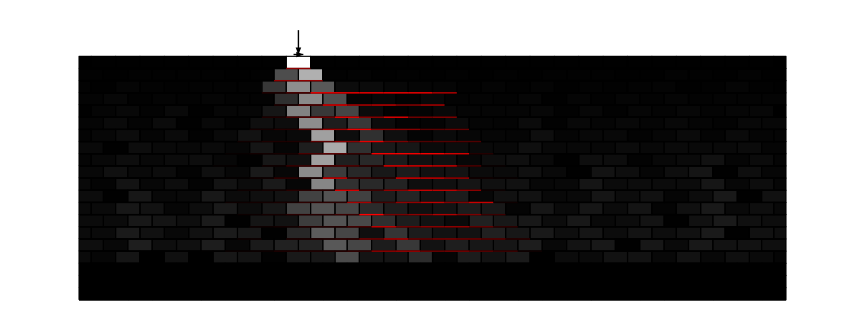

```mathematica
(*Solution*)
solveProblem[]
```

```mathematica
eqCheck
```

False

```mathematica
checkBlockEquilibrium[{nRow_,j_}]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,Vtot,Htot,Mtot},
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=getBlockLoads[{nRow,j}];

If[isBlockHalved[{nRow,j}],
Vtot=Vsu+Vsb+Ns+Nc+P/2+Nd-Vdu-Vdb-Rs-Rc-Rd;
Htot=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb-Vs-Vc-Vd;
If[isBlockOnLeftEdge[{nRow,j}],
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb-P/2/2)b/2-h(Lsu-Ldu+Ts+Tc+Td);,
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb+P/2/2)b/2-h(Lsu-Ldu+Ts+Tc+Td);
];,
Vtot=Vsu+Vsb+Ns+Nc+P+Nd-Vdu-Vdb-Rs-Rc-Rd;
Htot=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb-Vs-Vc-Vd;
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td);
];

{Vtot,Htot,Mtot}
];
```

```mathematica
c={};
For[nRow=1,nRow≤nely,nRow++,
For[j=1,j≤getTotalBlocksInRow[nRow],j++,
If[Chop[checkBlockEquilibrium[{nRow,j}],10^-3]≠{0,0,0},
AppendTo[c,{nRow,j}];
];
];
];
c
```

{{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19}}

```mathematica
r=15;
```

```mathematica
getBlockLoads[{r,getTotalBlocksInRow[r]}]
```

{0,0,0,0,0,0,0.951497,0.0269494,0,0,0,0,1.0015,0.0269494,0,0,0.00194941,0,0.025,0}

```mathematica
solveHalvedBlockL2R[getBlockLoads[{r,getTotalBlocksInRow[r]}],False]
```

{0,0,0,0,0,0,0.951497,0.0269494,0,0,0,0.,1.0015,0.025,0,0,0.00194941,0,0.,0}

```mathematica
contacts[[getBlockNum[{14,19}]]]
```

1

```mathematica
checkBlockEquilibrium[{15,20}]
```

{0.,-0.0269494,0.}

```mathematica
applyLoads[]
```

```mathematica
nRow=6;
```

```mathematica
solveRow[19]
```

$Aborted

```mathematica
transferContactActionsBelow[18]
```

```mathematica
blockSequence=findSolvableBlockSequence[nRow];
```

```mathematica
blockSequence["seq"][[2]]
```

{8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
For[j=1,j<=Length[blockSequence["seq"]],j++,
Do[
blockLoads=getBlockLoads[{nRow,k}];
contact=contacts[[getBlockNum[{nRow,k}]]];
blockLoads=solveBlock[blockLoads,contact,{nRow,k},blockSequence["dir"][[j]]];
updateStress[blockLoads,{nRow,k}];,
{k,blockSequence["seq"][[j]]}
];
];
```

```mathematica
σv[[getBlockNum[{6,10}]]]
```

{19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.}

```mathematica
getBlockLoads[{6,10}]
```

{0,0,0,0,19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.,0,0,0,0}

```mathematica
contacts[[getBlockNum[{6,10}]]]
```

3

```mathematica
solveBlock[getBlockLoads[{6,10}],3,{6,10},1]
```

{0,0,0,0,19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.,0,0,0,0}

```mathematica
checkBlockEquilibrium[{6,10}]//Chop
```

{0,0,-5.65706×10^-10}

```mathematica
unbalancedBlocksData=checkRowEquilibrium[nRow,blockSequence["cri"]];
```

```mathematica
unbalancedBlocksData["eq_check"]
```

True

```mathematica
(*equilibrium checks*)
If[unbalancedBlocksData["eq_check"]&&Length[unbalancedBlocksData["blocks"]]!=0,
(*start correcting unbalanced blocks*)
rowEqCheck=startCorrectionWaves[nRow,unbalancedBlocksData];,
(*no block needs correction*)
rowEqCheck=unbalancedBlocksData["eq_check"];
];

rowEqCheck
```

True